```mathematica
Mac
f = Import["/Users/newlocaluser/Documents/MP2/Data/sData/sofiaNormCrossOmega.mat","LabeledData"];
bciTraits = Import["/Users/newlocaluser/Documents/MP2/Data/David Data/bci.traits.csv"];
species = Import["/Users/newlocaluser/Documents/MP2/Code/species.csv"];
```

Mac

```mathematica
Windows

f=Import["C:/Users/Joel/Documents/CoMPLEX/MP2/sData/sofiaNormCrossOmega.mat","LabeledData"];
bciTraits = Import["C:/Users/Joel/Documents/CoMPLEX/MP2/bci.traits.csv"];
```

Windows

```mathematica
Data Purification
bciAdultNormCrossOmegas10 = Flatten[Values[Select[f,Keys[#]=="bciAdultNormCrossOmegas10"&]],1];
index14110 = Flatten[Values[Select[f,Keys[#]=="index141_10"&]]];
clusterIndices = Map[IntegerPart[#]&,Flatten[Values[Select[f,Keys[#]=="bciAdultClusterIndices10_5_141"&]]]];
B=MapThread[If[#2,MapThread[If[#2,#1,0]&,{#1,index14110}],ConstantArray[0,Length[#1]]]&,{bciAdultNormCrossOmegas10,index14110}];
clusterSpecies = DeleteCases[Flatten[MapIndexed[If[Length[DeleteCases[#,0]]>0,#2,0]&,B]],0];
clusters = Map[Keys[#]&,GatherBy[MapThread[#1->#2&,{clusterSpecies,clusterIndices}],Values[#]&]];
speciesMap = MapThread[#1->First[#2]&,{clusterSpecies,species}];
bciTraits[[2;;All,2]];
bciValid = Flatten[Select[MapIndexed[With[{name=First[#1],index=First[#2]},index->Flatten[Select[bciTraits,MemberQ[#,name]&],1]]&,species],Values[#]≠{}&],1];
```

Data Purification

```mathematica
Graph Construction

Manipulate[
A = DeleteDuplicates[DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1>adjacencyThreshold && i≠j,i->j,0]]&,#1]]&,B]],0]];
W = DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1>adjacencyThreshold && i≠j,#1,0]]&,#1]]&,B]],0];

An = DeleteDuplicates[DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1<-adjacencyThreshold && i≠j,i->j,0]]&,#1]]&,B]],0]];
Wn = DeleteCases[
Flatten[MapIndexed[With[{i=First[#2]},MapIndexed[With[{j=First[#2]},If[#1< -adjacencyThreshold && i≠j,#1,0]]&,#1]]&,B]],0];
validSpecies = DeleteDuplicates[Map[Keys[#]&,A]];
validClusters = Map[Intersection[#,validSpecies]&,clusters];
gn = Graph[An,DirectedEdges->True,EdgeWeight->Abs[Wn]];
gp =Graph[A,DirectedEdges->True,EdgeWeight->W];
g = Graph[Join[An,A],DirectedEdges->True,EdgeWeight->Join[Wn,W]];
{gp,gn,g}

,{adjacencyThreshold,2.75},ControlType->InputField]
```

Construction Graph

Anton

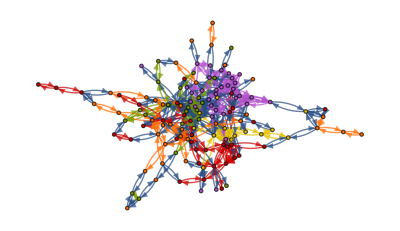

-Graphics-

```mathematica
Anton

HighlightGraph[g,Map[Subgraph[g,#]&,validClusters]]
CommunityGraphPlot[g,validClusters]
```

# Social Network Analysis

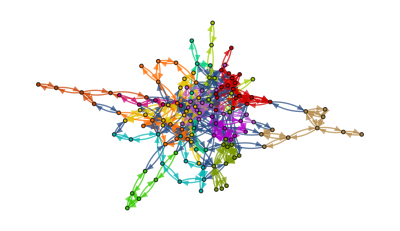

-Graphics-

```mathematica
communities = FindGraphCommunities[gp,Method->"Modularity"];
HighlightGraph[g,Map[Subgraph[g,#]&,communities]]
CommunityGraphPlot[g,communities]
```

```mathematica
ValidData[var_] := Not[MemberQ[Map[NumberQ[#]&,var],False]]
```

```mathematica
Trait Space
```

```mathematica
ReducedData = DimensionReduce[DeleteCases[Map[If[ValidData[Take[#,-3]],Take[#,{6,25}],Invalid]&,Values[bciValid]],Invalid],3];
```

```mathematica
Graphics3D[Map[Point[#]&,ReducedData],Axes->True]
```

-Graphics3D-